## Read in Data

```mathematica
(*File which contains all input data*)
SetDirectory["C:\\Users\\cgb36\\Dropbox (Cambridge University)\\iDirac - Wytham Final\\CamCan Model\\20190222_UpdatedModel"];
```

```mathematica
co2data = Import["All_CO2_forRod.csv","CSV"];
isoprene1data = Import["all_inlet1_G_isoprene.csv","CSV"];
isoprene2data = Import["all_inlet2_D_isoprene.csv","CSV"];
isoprene3data = Import["all_inlet3_W_isoprene.csv","CSV"];
isoprene4data = Import["all_inlet4_T_isoprene.csv","CSV"];
```

#### Set date range

```mathematica
t1=AbsoluteTime[{"27/07/2018",{"Day","Month","Year"}}];
t2=AbsoluteTime[{"07/08/2018",{"Day","Month","Year"}}];
```

```mathematica
t1a=t1+3600;
t2a = t2-3600;
```

## CO2 Logger Data

```mathematica
co2data[[1;;4]]//TableForm
```

1_DateTime | 1_AirT/C | 1_CO2_val | 2_DateTime | 2_AirT/C | 2_CO2_val | 3_DateTime | 3_AirT/C | 3_CO2_val | 4_DateTime | 4_AirT/C | 4_CO2_val
27/07/2018 00:00 | 22.7 | 423 | 27/07/2018 00:00 | 23.2 | 435 | 27/07/2018 00:00 | 22.9 | 405 | 27/07/2018 00:00 | 21.8 | 407
27/07/2018 00:01 | 22.7 | 426 | 27/07/2018 00:01 | 23.2 | 435 | 27/07/2018 00:01 | 22.9 | 404 | 27/07/2018 00:01 | 21.9 | 407
27/07/2018 00:02 | 22.6 | 424 | 27/07/2018 00:02 | 23.1 | 435 | 27/07/2018 00:02 | 22.9 | 404 | 27/07/2018 00:02 | 21.9 | 408

### CO2 Data

```mathematica
(*Create individual tables for CO2 at each inlet*)
co2data1=Table[{co2data[[i,1]],co2data[[i,3]]},{i,2,Length[co2data],60}];co2data2=Table[{co2data[[i,4]],co2data[[i,6]]},{i,2,Length[co2data],60}];co2data3=Table[{co2data[[i,7]],co2data[[i,9]]},{i,2,Length[co2data],60}];co2data4=Table[{co2data[[i,10]],co2data[[i,12]]},{i,2,Length[co2data],60}];
```

```mathematica
(*The following blocks check the data quality and removes any corrupt points from the CO2 data. It also converts the datetime to absolute time*)
```

```mathematica
flag = Table[0,{i,Length[co2data1]}];
Do[If[MatchQ[co2data1[[i,2]],_Integer],,flag[[i]]=1],{i,Length[co2data1]}]
Do[If[flag[[i]]>0.5, co2data1=Drop[co2data1,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data1[[i,1]]=AbsoluteTime[{co2data1[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data1]}]
```

```mathematica
flag = Table[0,{i,Length[co2data2]}];
Do[If[MatchQ[co2data2[[i,2]],_Integer],,flag[[i]]=1],{i,Length[co2data2]}]
Do[If[flag[[i]]>0.5, co2data2=Drop[co2data2,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data2[[i,1]]=AbsoluteTime[{co2data2[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data2]}]
```

```mathematica
flag = Table[0,{i,Length[co2data3]}];
Do[If[MatchQ[co2data3[[i,2]],_Integer],,flag[[i]]=1],{i,Length[co2data3]}]
Do[If[flag[[i]]>0.5, co2data3=Drop[co2data3,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data3[[i,1]]=AbsoluteTime[{co2data3[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data3]}]
```

```mathematica
flag = Table[0,{i,Length[co2data4]}];
Do[If[MatchQ[co2data4[[i,2]],_Integer],,flag[[i]]=1],{i,Length[co2data4]}]
Do[If[flag[[i]]>0.5, co2data4=Drop[co2data4,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data4[[i,1]]=AbsoluteTime[{co2data4[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data4]}]
```

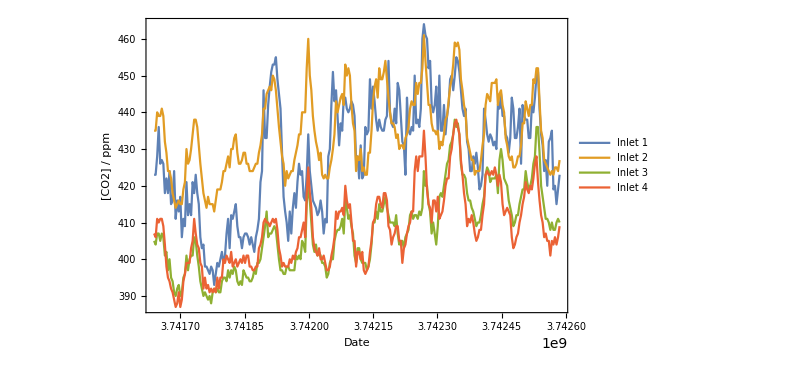

```mathematica
DateListPlot[{co2data1,co2data2,co2data3,co2data4},FrameLabel->{"Date","[CO2] / ppm"},LabelStyle->Directive[Bold, Medium],PlotLegends->{"Inlet 1","Inlet 2","Inlet 3","Inlet 4"},ImageSize->600]
```

### Temperature Data

```mathematica
(*These lines create individual tables for temperature (from co2 logger) at each inlet*)
co2data1t=Table[{co2data[[i,1]],co2data[[i,2]]},{i,2,Length[co2data],60}];co2data2t=Table[{co2data[[i,4]],co2data[[i,5]]},{i,2,Length[co2data],60}];co2data3t=Table[{co2data[[i,7]],co2data[[i,8]]},{i,2,Length[co2data],60}];co2data4t=Table[{co2data[[i,10]],co2data[[i,11]]},{i,2,Length[co2data],60}];
```

```mathematica
(*The following blocks check the data quality and removes any corrupt points from the temperature data. It also converts the datetime to absolute time*)
```

```mathematica
flag = Table[0,{i,Length[co2data1t]}];
Do[If[MatchQ[N[co2data1t[[i,2]]],_Real],,flag[[i]]=1],{i,Length[co2data1t]}]
Do[If[flag[[i]]>0.5, co2data1t=Drop[co2data1t,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data1t[[i,1]]=AbsoluteTime[{co2data1t[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data1t]}]
```

```mathematica
flag = Table[0,{i,Length[co2data2t]}];
Do[If[MatchQ[N[co2data2t[[i,2]]],_Real],,flag[[i]]=1],{i,Length[co2data2t]}]
Do[If[flag[[i]]>0.5, co2data2t=Drop[co2data2t,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data2t[[i,1]]=AbsoluteTime[{co2data2t[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data2t]}]
```

```mathematica
flag = Table[0,{i,Length[co2data3t]}];
Do[If[MatchQ[N[co2data3t[[i,2]]],_Real],,flag[[i]]=1],{i,Length[co2data3t]}]
Do[If[flag[[i]]>0.5, co2data3t=Drop[co2data3t,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data3t[[i,1]]=AbsoluteTime[{co2data3t[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data3t]}]
```

```mathematica
flag = Table[0,{i,Length[co2data4t]}];
Do[If[MatchQ[N[co2data4t[[i,2]]],_Real],,flag[[i]]=1],{i,Length[co2data4t]}]
Do[If[flag[[i]]>0.5, co2data4t=Drop[co2data4t,{i,i}]],{i,Length[flag],1,-1}]
Do[co2data4t[[i,1]]=AbsoluteTime[{co2data4t[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[co2data4t]}]
```

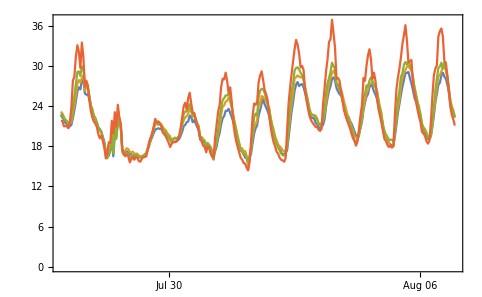

```mathematica
DateListPlot[{co2data1t,co2data2t,co2data3t,co2data4t}]
```

### Select data for time range t1a - t2a

```mathematica
Do[If[co2data1[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[co2data1]}];
Do[If[co2data1[[i,1]]>t2a,na2 = i;Break[]],{i,Length[co2data1]}];
co2h1=Take[co2data1,{na1,na2}];
co2h1t=Take[co2data1t,{na1,na2}];
```

```mathematica
Do[If[co2data2[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[co2data2]}];
Do[If[co2data2[[i,1]]>t2a,na2 = i;Break[]],{i,Length[co2data2]}];
co2h2=Take[co2data2,{na1,na2}];co2h2t=Take[co2data2t,{na1,na2}];
```

```mathematica
Do[If[co2data3[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[co2data3]}];
Do[If[co2data3[[i,1]]>t2a,na2 = i;Break[]],{i,Length[co2data3]}];
co2h3=Take[co2data3,{na1,na2}];co2h3t=Take[co2data3t,{na1,na2}];
```

```mathematica
Do[If[co2data4[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[co2data4]}];
Do[If[co2data4[[i,1]]>t2a,na2 = i;Break[]],{i,Length[co2data4]}];
co2h4=Take[co2data4,{na1,na2}];co2h4t=Take[co2data4t,{na1,na2}];
```

## Isoprene Data This section extracts the isoprene data, makes tables for each inlet, checks for quality, converts datetime to absolute time and selects the time period we want to look at.

```mathematica
isoprene1data[[1;;4]]//TableForm
```

1Abs_Time | 1Igor_time | 1Chrom_No | 1Volume | 1Isoprene_PH | 1Isoprene_Area | 1Isoprene_PH_ppb | 1Isoprene_Area_ppb
3739778239 | 05/07/2018 11:17 | 34894 | 150.06 | -5.32944 | -0.502456 | -0.0978718 | -0.121559
3739779599 | 05/07/2018 11:39 | 34896 | 150.18 | -8.44669 | -0.796349 | -0.15273 | -0.19099
3739780984 | 05/07/2018 12:03 | 34898 | 150.16 | -15.2058 | -1.4336 | -0.273569 | -0.343849

```mathematica
isoprenedata1=Table[{isoprene1data[[i,2]],isoprene1data[[i,8]]},{i,2,Length[isoprene1data],1}];isoprenedata2=Table[{isoprene2data[[i,2]],isoprene2data[[i,8]]},{i,2,Length[isoprene2data],1}];isoprenedata3=Table[{isoprene3data[[i,2]],isoprene3data[[i,8]]},{i,2,Length[isoprene3data],1}];isoprenedata4=Table[{isoprene4data[[i,2]],isoprene4data[[i,8]]},{i,2,Length[isoprene4data],1}];
```

```mathematica
flag = Table[0,{i,Length[isoprenedata1]}];
Do[If[MatchQ[isoprenedata1[[i,2]],_Real],,flag[[i]]=1],{i,Length[isoprenedata1]}]
Do[If[flag[[i]]>0.5, isoprenedata1=Drop[isoprenedata1,{i,i}]],{i,Length[flag],1,-1}]
Do[isoprenedata1[[i,1]]=AbsoluteTime[{isoprenedata1[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[isoprenedata1]}]
```

```mathematica
flag = Table[0,{i,Length[isoprenedata2]}];
Do[If[MatchQ[isoprenedata2[[i,2]],_Real],,flag[[i]]=1],{i,Length[isoprenedata2]}]
Do[If[flag[[i]]>0.5, isoprenedata2=Drop[isoprenedata2,{i,i}]],{i,Length[flag],1,-1}]
Do[isoprenedata2[[i,1]]=AbsoluteTime[{isoprenedata2[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[isoprenedata2]}]
```

```mathematica
flag = Table[0,{i,Length[isoprenedata3]}];
Do[If[MatchQ[isoprenedata3[[i,2]],_Real],,flag[[i]]=1],{i,Length[isoprenedata3]}]
Do[If[flag[[i]]>0.5, isoprenedata3=Drop[isoprenedata3,{i,i}]],{i,Length[flag],1,-1}]
Do[isoprenedata3[[i,1]]=AbsoluteTime[{isoprenedata3[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[isoprenedata3]}]
```

```mathematica
flag = Table[0,{i,Length[isoprenedata4]}];
Do[If[MatchQ[isoprenedata4[[i,2]],_Real],,flag[[i]]=1],{i,Length[isoprenedata4]}]
Do[If[flag[[i]]>0.5, isoprenedata4=Drop[isoprenedata4,{i,i}]],{i,Length[flag],1,-1}]
Do[isoprenedata4[[i,1]]=AbsoluteTime[{isoprenedata4[[i,1]],{"Day","Month","Year","Hour","Minute"}}],{i,Length[isoprenedata4]}]
```

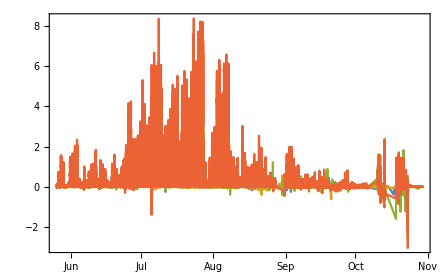

```mathematica
DateListPlot[{isoprenedata1,isoprenedata2,isoprenedata3,isoprenedata4},PlotRange->All]
```

```mathematica
Do[If[isoprenedata1[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[isoprenedata1]}];
Do[If[isoprenedata1[[i,1]]>t2a,na2 = i;Break[]],{i,Length[isoprenedata1]}];
isopreneh1=Take[isoprenedata1,{na1,na2}];
```

```mathematica
Do[If[isoprenedata2[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[isoprenedata2]}];
Do[If[isoprenedata2[[i,1]]>t2a,na2 = i;Break[]],{i,Length[isoprenedata2]}];
isopreneh2=Take[isoprenedata2,{na1,na2}];
```

```mathematica
Do[If[isoprenedata3[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[isoprenedata3]}];
Do[If[isoprenedata3[[i,1]]>t2a,na2 = i;Break[]],{i,Length[isoprenedata3]}];
isopreneh3=Take[isoprenedata3,{na1,na2}];
```

```mathematica
Do[If[isoprenedata4[[i,1]]>t1a,na1 = i-1;Break[]],{i,Length[isoprenedata4]}];
Do[If[isoprenedata4[[i,1]]>t2a,na2 = i;Break[]],{i,Length[isoprenedata4]}];
isopreneh4=Take[isoprenedata4,{na1,na2}];
```

### Smooth isoprene data to compare more easily

```mathematica
isopreneh1s=MeanFilter[isopreneh1[[All,2]],2];
isopreneh2s=MeanFilter[isopreneh2[[All,2]],2];
isopreneh3s=MeanFilter[isopreneh3[[All,2]],2];
isopreneh4s=MeanFilter[isopreneh4[[All,2]],2];
```

```mathematica
isopsmooth1=Table[{isopreneh1[[i,1]],isopreneh1s[[i]]},{i,Length[isopreneh1]}];
isopsmooth2=Table[{isopreneh2[[i,1]],isopreneh2s[[i]]},{i,Length[isopreneh2]}];
isopsmooth3=Table[{isopreneh3[[i,1]],isopreneh3s[[i]]},{i,Length[isopreneh3]}];
isopsmooth4=Table[{isopreneh4[[i,1]],isopreneh4s[[i]]},{i,Length[isopreneh4]}];
```

## Use PAR data to get a function of how PAR changes through the canopy

#### Import PAR data and plot

```mathematica
Directory[]
```

C:\Users\cgb36\Dropbox (Cambridge University)\iDirac - Wytham Final\CamCan Model\20190222_UpdatedModel

```mathematica
allpardata = Import["CR300_PAR_Table1_20180907.dat","CSV"];
```

```mathematica
allpardata[[1;;6]]//TableForm
```

TOA5 | CR300_PAR | CR300 | 11146 | CR300.Std.07.00 | CPU:CCSL018583_VF.CR300 | 36913 | Table1
TIMESTAMP | RECORD | BattV_Avg | PTemp_C_Avg | PFF_5m_1_Avg | PFF_5m_2_Avg | PFF_10m_Avg | PFF_15m_Avg
TS | RN | Volts | Deg C | umol/m-2/s-1 | umol/m-2/s-1 | umol/m-2/s-1 | umol/m-2/s-1
 |  | Avg | Avg | Avg | Avg | Avg | Avg
2018-08-21 11:10:00 | 675 | 12.14 | 23.41 | 6.616 | 10.52 | 6.333 | 4.124
2018-08-21 11:12:00 | 676 | 12.15 | 23.45 | 6.556 | 10.5 | 6.316 | 4.151

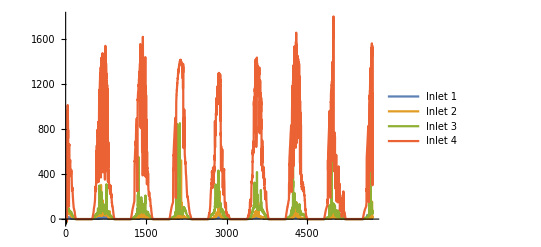

```mathematica
ListLinePlot[{allpardata[[5;;,8]],allpardata[[5;;,7]],allpardata[[5;;,6]],allpardata[[5;;,5]]},PlotRange->All,PlotLegends->{"Inlet 1","Inlet 2","Inlet 3","Inlet 4"}]
```

#### Tidy PAR data

```mathematica
(*Select PAR values and put inlets in order*)
pardata=Table[{allpardata[[i,1]],allpardata[[i,8]],allpardata[[i,7]],allpardata[[i,6]],allpardata[[i,5]]},{i,5,Length[allpardata]}];
pardata[[1;;3]]//TableForm
```

2018-08-21 11:10:00 | 4.124 | 6.333 | 10.52 | 6.616
2018-08-21 11:12:00 | 4.151 | 6.316 | 10.5 | 6.556
2018-08-21 11:14:00 | 4.18 | 6.329 | 10.5 | 6.625

```mathematica
(*Get rid of NA values in each column*)
flag = Table[0,{i,Length[pardata]}];
Do[If[MatchQ[N[pardata[[i,2]]],_Real],,flag[[i]]=1],{i,Length[pardata]}]
Do[If[flag[[i]]>0.5, pardata=Drop[pardata,{i,i}]],{i,Length[flag],1,-1}]

flag = Table[0,{i,Length[pardata]}];
Do[If[MatchQ[N[pardata[[i,3]]],_Real],,flag[[i]]=1],{i,Length[pardata]}]
Do[If[flag[[i]]>0.5, pardata=Drop[pardata,{i,i}]],{i,Length[flag],1,-1}]

flag = Table[0,{i,Length[pardata]}];
Do[If[MatchQ[N[pardata[[i,4]]],_Real],,flag[[i]]=1],{i,Length[pardata]}]
Do[If[flag[[i]]>0.5, pardata=Drop[pardata,{i,i}]],{i,Length[flag],1,-1}]

flag = Table[0,{i,Length[pardata]}];
Do[If[MatchQ[N[pardata[[i,5]]],_Real],,flag[[i]]=1],{i,Length[pardata]}]
Do[If[flag[[i]]>0.5, pardata=Drop[pardata,{i,i}]],{i,Length[flag],1,-1}]
```

#### Calculate mean for each inlet and make function of PAR vs box number

```mathematica
(*Calculate mean for each inlet*)
mean1=Mean[pardata[[All,2]]];
mean2=Mean[pardata[[All,3]]];
mean3=Mean[pardata[[All,4]]];
mean4=Mean[pardata[[All,5]]];
```

```mathematica
(*Combine means into list, scale so that top of canopy = 1*)
meanPAR={mean1,mean2,mean3,mean4};
meanPARscaled=meanPAR/mean4;

boxno={1,13,22,26};
```

```mathematica
parvsbox=Transpose[{boxno,meanPARscaled}];
```

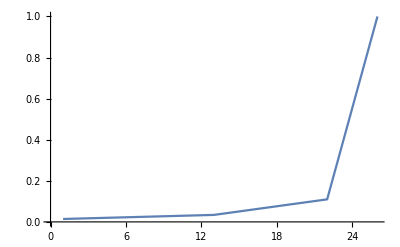

```mathematica
ListLinePlot[parvsbox]
```

```mathematica
(*Add values for top of model above canopy where PAR is constant and =1*)
par2=Join[meanPARscaled ,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}];
boxno2=Join[boxno,{27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}];
parvsbox2=Transpose[{boxno2,par2}];
```

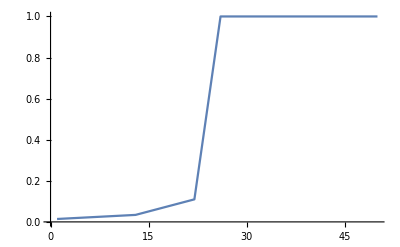

```mathematica
(*Interpolate to get function of PAR through canopy*)
pari=Interpolation[parvsbox2,InterpolationOrder->1];
ListLinePlot[pari]
```

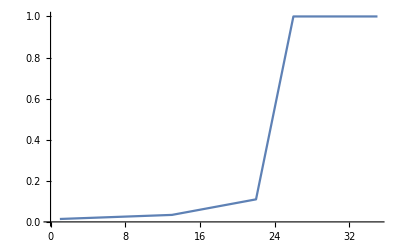

```mathematica
testpar=Table[pari[i],{i,1,35}];
ListLinePlot[testpar]
```

## Plots of Selected Periods

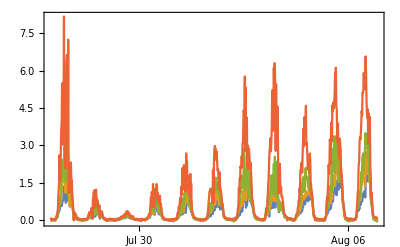

```mathematica
DateListPlot[{isopreneh1,isopreneh2,isopreneh3,isopreneh4},PlotRange->All]
```

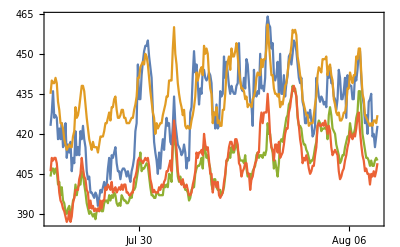

```mathematica
DateListPlot[{co2h1,co2h2,co2h3,co2h4},PlotRange->All]
```

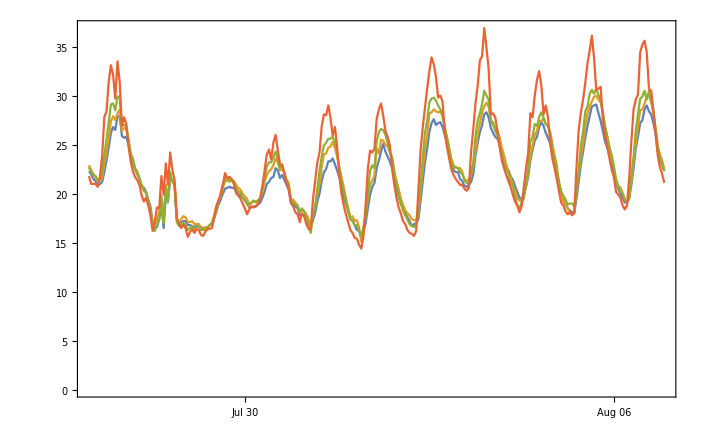

```mathematica
DateListPlot[{co2h1t,co2h2t,co2h3t,co2h4t},PlotRange->All]
```

## Reading in Meteorological Data

```mathematica
Directory[]
```

C:\Users\cgb36\Dropbox (Cambridge University)\iDirac - Wytham Final\CamCan Model\20190222_UpdatedModel

```mathematica
met = Import["simple_met_abstime.csv","CSV"];
```

```mathematica
met[[1]]
```

{datetime,nsec,record,solrad,netrad,rh,temp,ws,wd,rain,albedsky,albedgrd,tempscreen,soil10,soil30,surfwet,soilmoist,mintemp,maxtemp,maxwind,battvol}

```mathematica
(*Creates a table of the absolute time from the met data*)
mettime = Table[AbsoluteTime[met[[i,2]]],{i,2,Length[met]}];

(*m1 and m2 are indicies of t1a and t2a in the met dataset, used below to select date range*)
Do[If[mettime[[i]]>t1,m1 = i-1;Break[]],{i,Length[mettime]}]
Do[If[mettime[[i]]>t2,m2= i;Break[]],{i,Length[mettime]}]
```

#### Temperature

```mathematica
mettemp=Table[{mettime[[i]],met[[i+1,7]]},{i,Length[mettime]}];
mtemp =Take[mettemp,{m1,m2}];
```

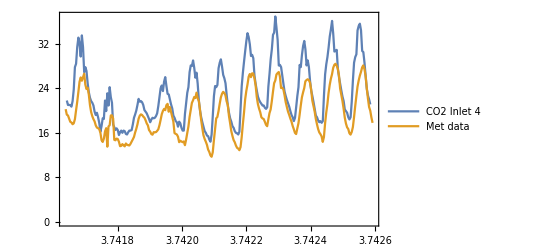

```mathematica
(*Compare the temperature from the inboard temperature probes on CO2 logger and the met station*)
DateListPlot[{co2h4t,mtemp},PlotRange->All,PlotLegends->{"CO2 Inlet 4","Met data"}]
```

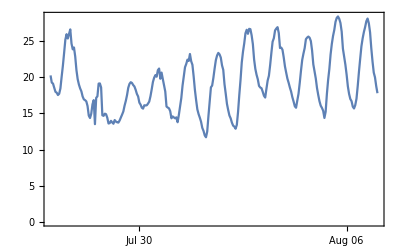

```mathematica
DateListPlot[{mtemp},PlotRange->All]
```

#### Wind Speed

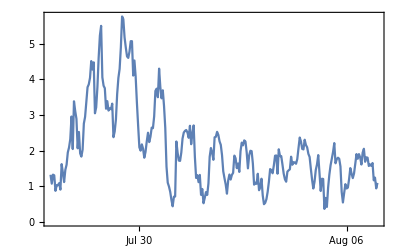

```mathematica
metspd=Table[{mettime[[i]],met[[i+1,8]]},{i,Length[mettime]}];
mspd =Take[metspd,{m1,m2}];
DateListPlot[{mspd},PlotRange->All]
```

#### Manipulating wind speed to use as proxy for diffusion coefficient

```mathematica
mspd2=Table[{mspd[[i,1]],mspd[[i,2]]*16/6+5},{i,Length[mspd]}];
```

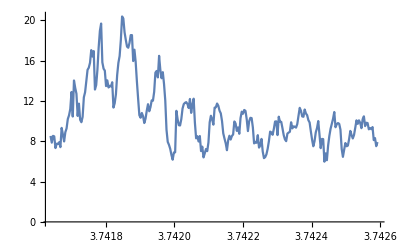

```mathematica
winspdi=Interpolation[mspd2];
ListLinePlot[winspdi]
```

#### Wind Direction

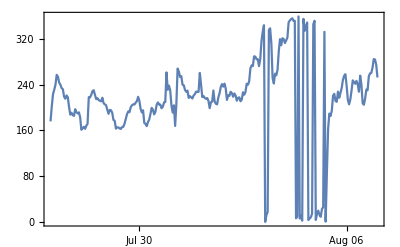

```mathematica
metdir=Table[{mettime[[i]],met[[i+1,9]]},{i,Length[mettime]}];
mdir =Take[metdir,{m1,m2}];
DateListPlot[{mdir},PlotRange->All]
```

#### Solar Radiation

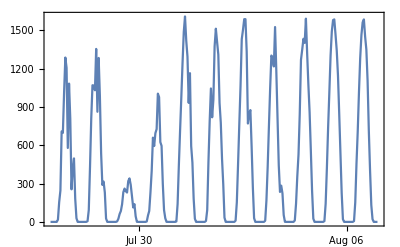

```mathematica
metsun=Table[{mettime[[i]],met[[i+1,4]]*4.6/2.4},{i,Length[mettime]}]; 
(*Conversion factor from solrad to PAR *4.6/2.4*)
msun=Take[metsun,{m1,m2}];
DateListPlot[{msun},PlotRange->All]
```

#### Interpolate solar radiation data to use as proxy for PAR

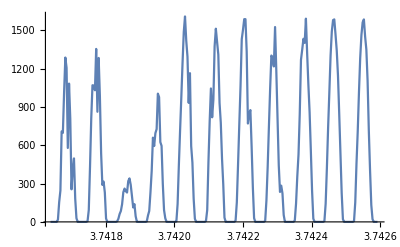

```mathematica
msuni=Interpolation[msun,InterpolationOrder->1];
ListLinePlot[msuni]
```

## Solar Altitude Angle

```mathematica
(*Creates a list of absolute times, spaced by 30mins*)
timeint = Table[i,{i,t1-3600,t2+3600,30*60}];
```

```mathematica
(*Creates a table of time vs the solar altitude angle, for that location, for interval timeint*)
solaltitude=Table[{timeint[[i]],SunPosition[GeoPosition[{51.773330,-1.338430}],DateObject[DateList[timeint[[i]]],TimeZone->0]][[2]]},{i,Length[timeint]}];
```

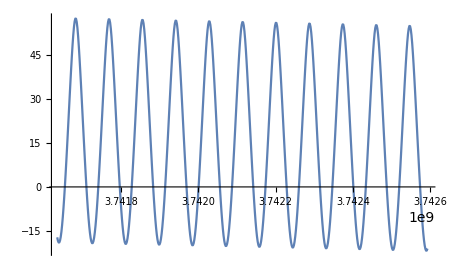

```mathematica
ListLinePlot[solaltitude]
```

```mathematica
(*This line converts that angle to a real number*)
realdeg = Table[{solaltitude[[i,1]],ToExpression[StringSplit[ToString[solaltitude[[i,2]]]," "][[1]]]},{i,Length[solaltitude]}];
```

#### Solar Zenith Angle

```mathematica
(*Solar zenith angle is 90 - solar altitude. Use cos to make into real number*)
solzen=Table[{solaltitude[[i,1]],Cos[90 Degree-solaltitude[[i,2]]]},{i,Length[solaltitude]}];
```

```mathematica
solzen[[1;;4]]//TableForm
```

3741634800 | -0.2949
3741636600 | -0.3143
3741638400 | -0.3239
3741640200 | -0.3235

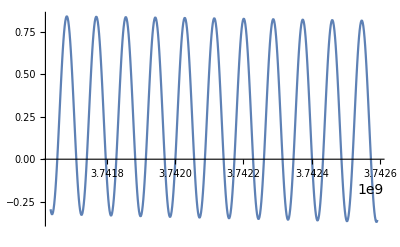

```mathematica
ListLinePlot[solzen]
```

```mathematica
solzeni=Interpolation[solzen];
```

## Chemical Reactions

#### Constants

```mathematica
(*Inert body concentration in atmosphere*)
m = 2.5 10^19;
```

```mathematica
(*Factor for converting to mixing ratio*)
ppb = 10^-9;
```

```mathematica
(*ozone mixing ratio converted to ppb*)
o3x = 30.*m*ppb
```

7.5×10^11

```mathematica
(*CO mixing ratio converted to ppb*)
cox = 200.*m*ppb;
```

### Ozone to O1D

```mathematica
(*This function determines the photolysis of O3 to O1d to get O1d photolysis constant, J and says that when the sun is beyond the horizon, it is 0*)
(*Where do the numbers come from?*)
po3to1d[t_]:=If[solzeni[t]>0,8.10^-05*(solzeni[t]^1.6)*Exp[-0.56/solzeni[t]],0.];
```

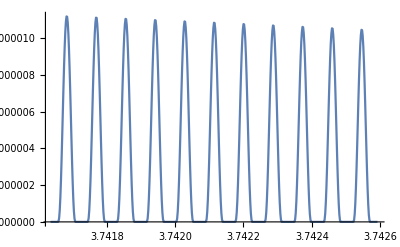

```mathematica
jo1d = Table[{timeint[[i]], po3to1d[timeint[[i]]]},{i,Length[timeint]}];
ListLinePlot[jo1d]
```

```mathematica
jo1di=Interpolation[jo1d];
```

#### Reactions involving O1D

```mathematica
(*O3 + hv -jO3-> O1d + O2*) (*B4 notes*)
jO3=2.5*10^-6;
(*O1d + M -k2-> O3p + M*) (*B4 notes*)
k2=3*10^-11;
(*Fraction of O1D molecules which react with water*)
f=0.1;
(*O1d + H2O -k1-> 2 OH*) (*B4 notes, fraction of reacted to o3p*)
k1=f*k2;
```

```mathematica
(*Find steady state conc of O1D*)
```

```mathematica
o1dconc=jO3*o3x/(k2*m)
```

0.0025

```mathematica
(*need to change this based on sunrise/sunset*)
```

#### Reactions involving OH

```mathematica
(*OH + CO -> CO2 + H, then fast H + O2 -> HO2, formation of HO2 radicals*)
k5 = 1.44 10^-13 (1+0.8m/(4.2 10^19))
```

2.12571×10^-13

```mathematica
(*OH + isoprene -> products*)
kisop=1.0 10^-12;
```

#### Reactions involving HO2

```mathematica
(*Source for these numbers?*)
k4 = 1.8 10^-12;
k3 = 2.32 10^-15;
```

```mathematica
ho2x = Sqrt[jO3*o3x*f/k4]
```

3.22749×10^8

```mathematica
Ho2x[jo3_]:= Sqrt[jo3*o3x*f/k4]
```

#### OH concentration variation over time (updated)

```mathematica
(*Function for calculating the concentration of OH*)
OHconc[jo3_]:=(2*f*jo3*o3x+k3*Ho2x[jo3]*o3x)/(k5*cox)
```

```mathematica
(*Plot of the OH conc over time*)
ohx= Table[{jo1d[[i,1]],OHconc[jo1d[[i,2]]]},{i,Length[jo1d]}];
```

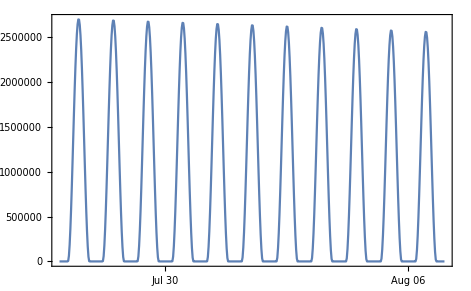

```mathematica
DateListPlot[ohx]
```

```mathematica
ohxi=Interpolation[ohx];
```

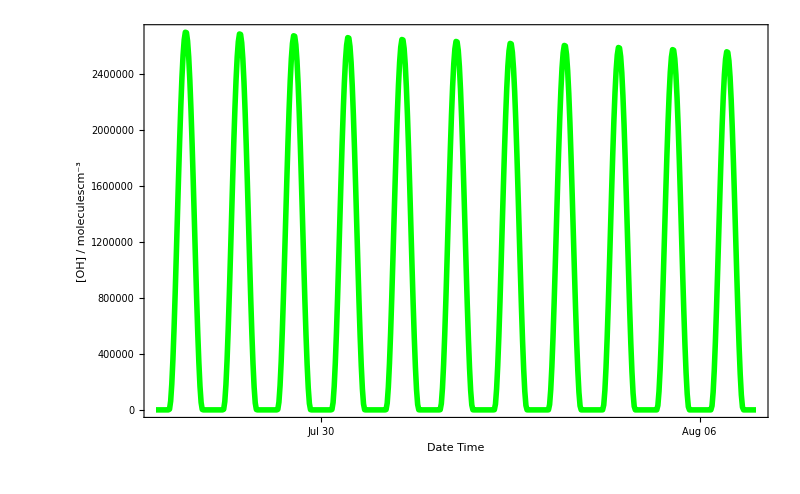

```mathematica
ohconcplot=DateListPlot[ohx,
Frame-> {True,True,False,False},
FrameLabel->{Style["Date Time",Black,32],Style["[OH] / moleculescm^-3",Black,32]},
LabelStyle->Directive[Black, 32],
PlotStyle->{Thickness[0.005],Green},
ImageSize->800,
PlotRange->All,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["OHconcplot.jpeg",ohconcplot]
```

OHconcplot.jpeg

## Diffusion

```mathematica
vkc=0.41;(*von karman constant*)
uval=5.0 ; (*wind speed*)
h=16.;(*canopy height *)
d=0.63*h; (*zero plane displacement*)
z0=0.13*h; (*roughness length*)
x=20.;(*reference height for wind speed*)
n=2.5;(*typical value for agricultural crops*)
```

```mathematica
LAIcum={3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.60,3.59,3.57,3.53,3.47,3.37,3.23,3.01,2.71,2.35,1.89,1.28,0.55,0.06,0.00,0.00,0.00,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
hos=16; (*overstory height, taken to be top of canopy*)
tT=4;(*ratio for canopy*)
r=((1-Exp[-tT])*(tT-1)^(1.5))/((tT-1+Exp[-tT])^1.5)(*near field correction*)
```

0.972762

```mathematica
(*define friction velocity*) 
Ustar[ureal_]:=vkc*ureal/Log[(x-d)/z0];
```

```mathematica
(*friction velocity scaled through canopy by leaf area index*)
Ustarleaf[windval_,j_]:=Ustar[windval]*Exp[−LAIcum[[j]]/2]
```

```mathematica
Sigmaw[windval_,j_]:=(1.25*Ustarleaf[windval,j])^2 (* vertical wind speed standard variance*)
Tl[windval_,j_]:=(0.3*h)/Ustarleaf[windval,j]
```

```mathematica
Kdiff[windval_,j_]:=r*0.3*(1.25^2)*h*Ustarleaf[windval,j]
```

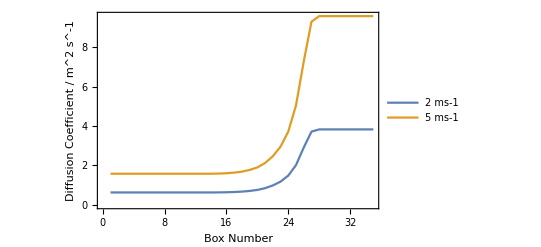

```mathematica
ListLinePlot[{Table[Kdiff[2,i],{i,35}],Table[Kdiff[5,i],{i,35}]},PlotLegends->Placed[{"2 ms-1","5 ms-1"},{0.2,0.9}],Frame-> {True,True,False,False},FrameLabel->{"Box Number","Diffusion Coefficient / m^2 s^-1"},LabelStyle->Directive[Bold, Medium]]
```

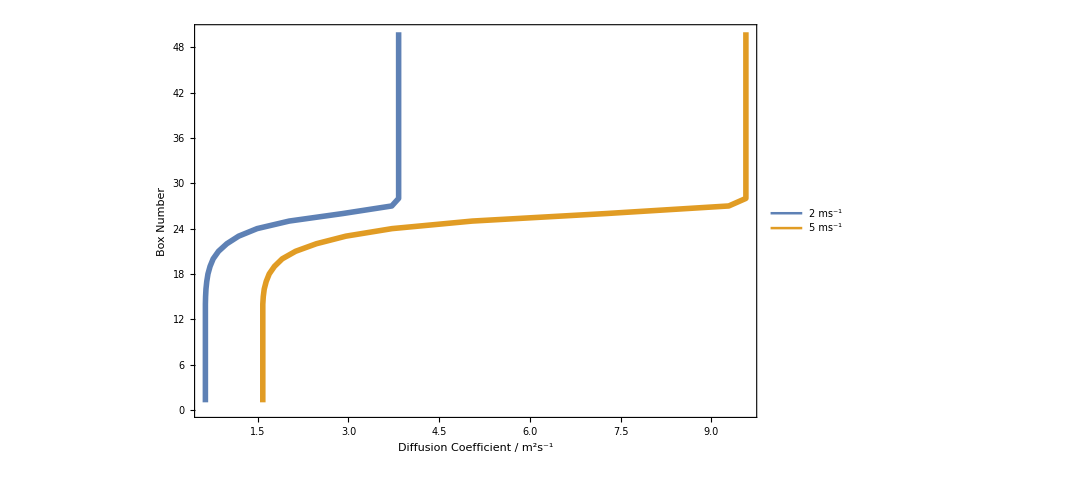

```mathematica
kdiffboxesplot=ListLinePlot[{Table[{Kdiff[2,i],i},{i,50}],Table[{Kdiff[5,i],i},{i,50}]},
PlotLegends->Placed[{"2 ms^-1","5 ms^-1"},{0.8,0.2}],
Frame-> {True,True,False,False},
PlotStyle->{Thickness[0.005],Thickness[0.005]},
FrameLabel->{Style["Diffusion Coefficient / m^2s^-1",Black,32],Style["Box Number",Black,32]},
LabelStyle->Directive[Black, 32],
ImageSize->800,
PlotRange->All,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["kdiffboxesplot.jpeg",kdiffboxesplot]
```

kdiffboxesplot.jpeg

#### Manipulating wind speed to use in diffusion coefficient

```mathematica
mspd2=MeanFilter[mspd[[All,2]],3];
```

```mathematica
mspd2i=Interpolation[mspd2];
```

```mathematica
mspd2a=Table[{mspd[[i,1]],mspd2[[i]]},{i,Length[mspd]}];
```

```mathematica
winspdi=Interpolation[mspd2a];
```

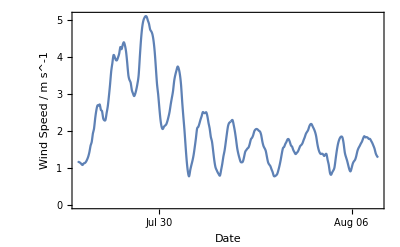

```mathematica
DateListPlot[Table[{t,winspdi[t]},{t,t1a,t2a,60}],Frame-> {True,True,False,False},FrameLabel->{"Date","Wind Speed / m s^-1"},LabelStyle->Directive[Bold, Medium]]
```

#### Use wind data in Kdiff function

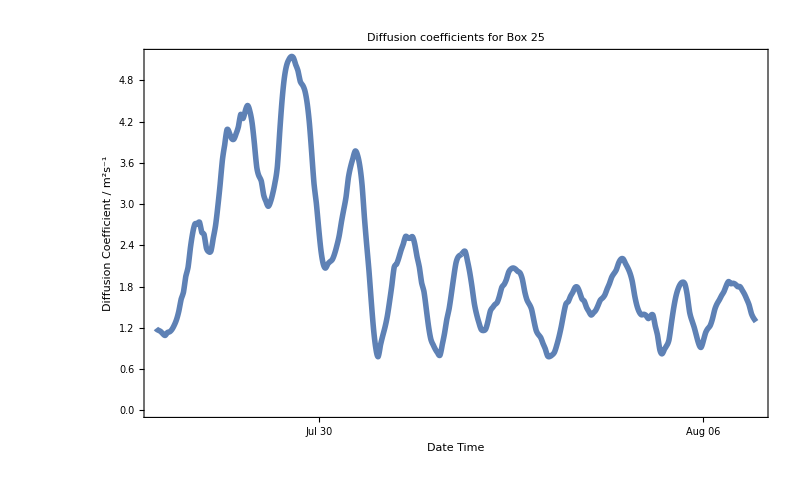

```mathematica
winddiffs=Table[{t,Kdiff[winspdi[t],25]},{t,t1a,t2a,60}];
kdiffwindplot=DateListPlot[winddiffs,
Frame-> {True,True,False,False},
PlotLabel->"Diffusion coefficients for Box 25",Frame-> {True,True,False,False},
FrameLabel->{Style["Date Time",Black,32],Style["Diffusion Coefficient / m^2s^-1",Black,32]},
LabelStyle->Directive[Black, 32],
ImageSize->800,
PlotStyle->{Thickness[0.005]},
PlotRange->All,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["kdiffwindplot.jpeg",kdiffwindplot]
```

kdiffwindplot.jpeg

```mathematica
windboxdiffs=Flatten[Table[{t,j,Kdiff[winspdi[t],j]},{t,t1a,t2a,60},{j,1,50}],1];
```

```mathematica
(*This is the diffusion constant, which we assume is at a maximum during the day with less diffusion during the night*)
kdiffi=Interpolation[windboxdiffs];
```

```mathematica
Plot3D[kdiffi[t,j],{t,t1a,t2a},{j,1,50},PlotRange->All]
```

-Graphics3D-

## Thinking About A Flux Model

#### Model parameters

```mathematica
(*Height in cm*) 
hgt = 3000;
(*The box heights in cm*)
dz = 60;
(*Number of boxes*)
nbox = hgt/dz
```

50

```mathematica
delz=dz/100.
```

0.6

```mathematica
boxvol=delz*1*1;
```

```mathematica
(*rate of deposition*)
kdep = 0.1;
```

```mathematica
daysec=24*3600;
```

```mathematica
(*Number of days in the data series*)
nd=Round[N[(t2a-t1a)/daysec]]
```

11

```mathematica
nbox
```

50

#### PAR variation through canopy

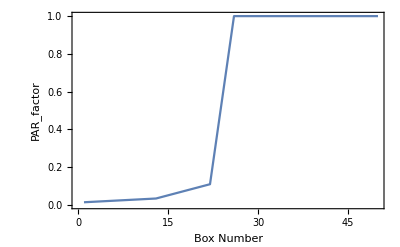

```mathematica
(*using par interpolation*)
jfactor = Table[pari[i],{i,nbox}];
ListLinePlot[{jfactor},Frame-> {True,True,False,False},FrameLabel->{"Box Number","PAR_factor"},LabelStyle->Directive[Bold, Medium]]
```

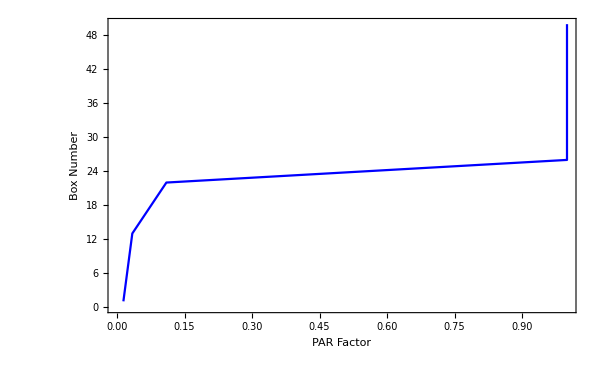

```mathematica
parfactplot=ListLinePlot[Table[{jfactor[[i]],i},{i,50}],
Frame-> {True,True,False,False},
FrameLabel->{Style["PAR Factor",Black,32],Style["Box Number",Black,32]},
LabelStyle->Directive[Black, 32],
PlotStyle->{Blue},
ImageSize->600,
PlotRange->All,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["parfactplot.jpeg",parfactplot]
```

parfactplot.jpeg

#### Leaf area variation through canopy

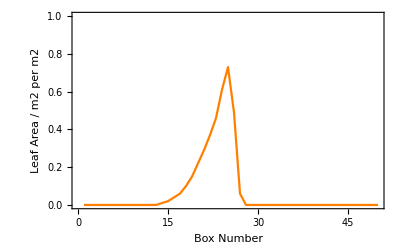

```mathematica
(*input values of leaf area by estimating no of leaves*)
leafarea = {0,0,0,0,0,0,0,0,0,0,0,0,0,0.01,0.02,0.04,0.06,0.10,0.15,0.22,0.29,0.37,0.46,0.61,0.73,0.49,0.06,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ListLinePlot[{leafarea},Frame-> {True,True,False,False},PlotStyle->{Orange},PlotRange->{0,1},FrameLabel->{"Box Number","Leaf Area / m2 per m2"},LabelStyle->Directive[Bold, Medium]]
```

```mathematica
leafarea[[25]]
```

0.73

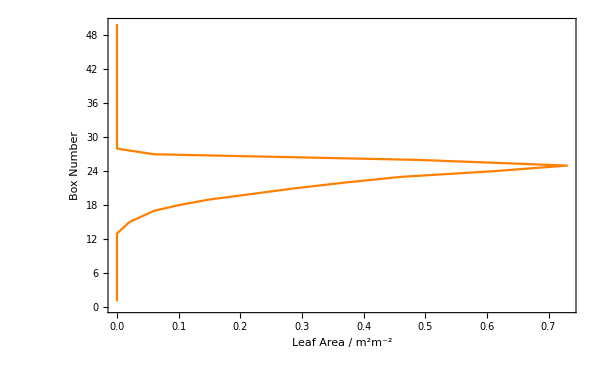

```mathematica
leafareaplot=ListLinePlot[Table[{leafarea[[i]],i},{i,50}],
Frame-> {True,True,False,False},
FrameLabel->{Style["Leaf Area / m^2m^-2",Black,32],Style["Box Number",Black,32]},
LabelStyle->Directive[Black, 32],
PlotStyle->{Orange},
ImageSize->600,
PlotRange->All,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["leafareaplot.jpeg",leafareaplot]
```

leafareaplot.jpeg

#### Temperature data manipulation to put into isopemiss function

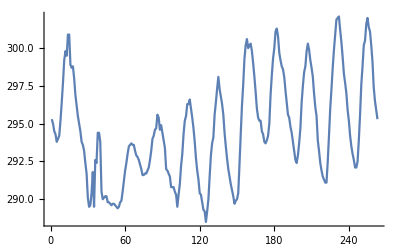

```mathematica
(*convert temperature to kelvin*)
tempk=Table[co2h1t[[i,2]]+273,{i,Length[co2h1t]}];
ListLinePlot[tempk]
```

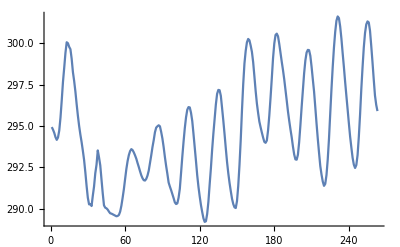

```mathematica
(*make curve smooth*)
tempk2=MeanFilter[tempk,2];
ListLinePlot[tempk2]
```

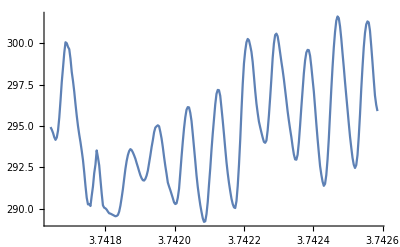

```mathematica
tempk3=Table[{co2h1t[[i,1]],tempk2[[i]]},{i,Length[co2h1t]}];
ListLinePlot[tempk3]
```

```mathematica
tempk3i=Interpolation[tempk3];
ListLinePlot[tempk3i]
```

-Graphics-

## Isoprene emission function

#### Define constants from emission rate equation

```mathematica
(*isoprene rate at standard temp and PAR, molec m-2 s-1 *)
(*converted to ppb per m2 per sec(?) *)
isopconst=(10^9/(2.53*10^25))*(6*10^15)/boxvol
```

0.395257

```mathematica
alpha=0.0027;
cl1=1.066;
temps=303;
tempm=314;
ct1=95000;
ct2=230000;
R=8.3145;
```

```mathematica
(*Make function CL which takes PAR and box number as input*)
parconst[L_,j_]:=(alpha*cl1*L*pari[j])/Sqrt[1+alpha^2*(L*pari[j])^2]
```

```mathematica
(*Make function CT which takes temperature as input*)
tempconst[T_]:=(Exp[ct1*(T-temps)/(R*temps*T)])/(1+Exp[ct2*(T-tempm)/(R*temps*T)])
```

#### Make overall isoprene emissions function which takes PAR, box and temp input

```mathematica
isopemiss[L_,T_,j_]:=isopconst*parconst[L,j]*tempconst[T]+RandomReal[0.0001]
```

```mathematica
isopemissall=Flatten[Table[{t,j,isopemiss[msuni[t],tempk3i[t],j]},{t,t1a,t2a,60},{j,1,nbox}],1];
```

```mathematica
(*Interpolated isoprene emission as function of temperature and box number*)
intisop=Interpolation[isopemissall];
```

## 3D plots of isoprene emission function

```mathematica
(*Plot using isopemissall data*)
Plot3D[isopemiss[msuni[t],tempk3i[t],j],{t,t1a,t1a+(3600*24*5)},{j,1,nbox},PlotRange->All]
```

-Graphics3D-

```mathematica
(*Plot using data from isopemissplot*)
isopemissplot=Flatten[Table[{t,j,isopemiss[msuni[t],tempk3i[t],j]},{t,t1a,t1a+(3600*24*3),60},{j,1,nbox}],1];
```

```mathematica
ListPlot3D[isopemissplot,PlotRange->All]
```

-Graphics3D-

```mathematica
(*Overall plot of isoprene emission function vs PAR and temperature*)
Plot3D[isopemiss[L,T,30],{T,298,338},{L,1,2000},AxesLabel->{"Temperature/K", "PAR/umol m-1 s-1","Emission rate / ppb m-1 s-1"}]
```

-Graphics3D-

## Equations for processes in boxes

### These equations describe the processes in the boxes

```mathematica
(*These are the important equations that describe the processes in any of the boxes*)
```

```mathematica
(*Box 1, doesn't have transport from below*) (*the 2 is nonsenseish*)
eqns1a={isop[ 1]'[t] == leafarea [[1]]*intisop[t,1]-kisop*ohxi[t]*isop[1][t]-(*leaffactor[[1]]**)(kdiffi[t,1]*(isop[ 1][t] - isop[ 2][t]))/(delz^2) -kdep*2*isop[1][t]};
```

```mathematica
(*box 2 to nbox - 1*)
eqns1b = Table[isop[ j]'[t] ==leafarea[[j]]*intisop[t,j]-kisop*ohxi[t]*isop[j][t]+(*leaffactor[[j]]**)(kdiffi[t,j]*(isop[ j-1][t] +isop[ j+1][t] - 2*isop[ j][t]))/(delz^2), {j, 2, nbox - 1}];
```

```mathematica
(*nbox, doesn't have transport upwards. Assumes box above nbox is zero*)
eqns1c={isop[nbox]'[t] == leafarea [[nbox]]*intisop[t,nbox]-kisop*ohxi[t]*isop[nbox][t]+ (*leaffactor[[nbox]]**)(kdiffi[t,nbox]*(isop[ nbox-1][t] - 2*isop[ nbox][t]))/(delz^2) };
```

```mathematica
eqns=Join[eqns1a,eqns1b,eqns1c];
```

#### Set up to solve differential equations

```mathematica
(*Set initial isoprene value at t1a to 0.1 for all boxes*)
inits= Flatten[Table[isop[j][t1a]==0.1,{j,1,nbox}]];
```

```mathematica
vars = Flatten[Table[{isop[j]},{j,1,nbox}]];
```

```mathematica
isopmodel= Join[eqns,inits];
```

```mathematica
Dimensions[isopmodel]
```

{100}

```mathematica
results1=NDSolve[isopmodel,vars,{t,t1a,t2a}];
```

```mathematica
Dimensions[results1]
```

{1,50}

## Results

```mathematica
box1=Table[{i,results1[[1,1,2]][i]},{i,t1a,t2a,1800}];
box3=Table[{i,results1[[1,3,2]][i]},{i,t1a,t2a,1800}];
box5=Table[{i,results1[[1,5,2]][i]},{i,t1a,t2a,1800}];
box6=Table[{i,results1[[1,6,2]][i]},{i,t1a,t2a,1800}];
box7=Table[{i,results1[[1,7,2]][i]},{i,t1a,t2a,1800}];
box9=Table[{i,results1[[1,9,2]][i]},{i,t1a,t2a,1800}];
box11=Table[{i,results1[[1,11,2]][i]},{i,t1a,t2a,1800}];
box13=Table[{i,results1[[1,13,2]][i]},{i,t1a,t2a,1800}];
box15=Table[{i,results1[[1,15,2]][i]},{i,t1a,t2a,1800}];
box16=Table[{i,results1[[1,16,2]][i]},{i,t1a,t2a,1800}];
box17=Table[{i,results1[[1,17,2]][i]},{i,t1a,t2a,1800}];
box19=Table[{i,results1[[1,19,2]][i]},{i,t1a,t2a,1800}];
box21=Table[{i,results1[[1,21,2]][i]},{i,t1a,t2a,1800}];
box22=Table[{i,results1[[1,22,2]][i]},{i,t1a,t2a,1800}];
box23=Table[{i,results1[[1,23,2]][i]},{i,t1a,t2a,1800}];
box25=Table[{i,results1[[1,25,2]][i]},{i,t1a,t2a,1800}];
box26=Table[{i,results1[[1,27,2]][i]},{i,t1a,t2a,1800}];
box27=Table[{i,results1[[1,27,2]][i]},{i,t1a,t2a,1800}];
box28=Table[{i,results1[[1,28,2]][i]},{i,t1a,t2a,1800}];
box29=Table[{i,results1[[1,29,2]][i]},{i,t1a,t2a,1800}];
box30=Table[{i,results1[[1,30,2]][i]},{i,t1a,t2a,1800}];
```

```mathematica
ColorData["Gradients"];
```

```mathematica
mycolor=ColorData["Rainbow"];
refcounter=Table[i/30.,{i,30}];
```

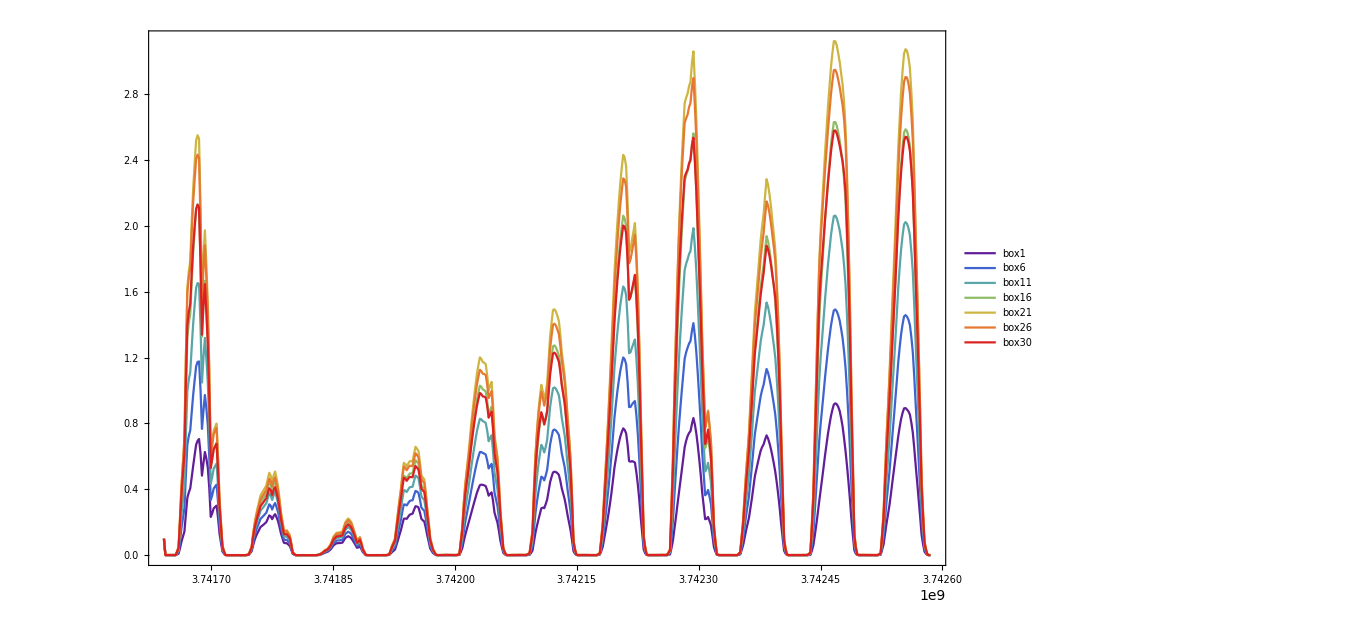

```mathematica
DateListPlot[{box1,box6,box11,box16,box21,box26,box30},PlotRange->All,PlotLegends->{"box1", "box6","box11","box16","box21","box26","box30"},ImageSize->1000,PlotStyle->{mycolor[refcounter[[1]]],mycolor[refcounter[[6]]],mycolor[refcounter[[11]]],mycolor[refcounter[[16]]],mycolor[refcounter[[21]]],mycolor[refcounter[[26]]],mycolor[refcounter[[30]]]}]
```

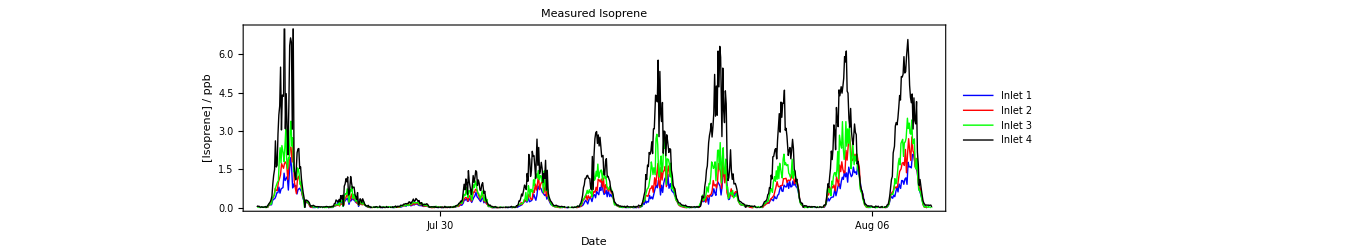

```mathematica
plot1=DateListPlot[{isopreneh1,isopreneh2,isopreneh3,isopreneh4},PlotRange->{Automatic,{0,7.0}}, PlotLabel-> "Measured Isoprene", LabelStyle -> Directive[Bold,14,FontFamily->"Arial"],PlotStyle->{Directive[Blue,AbsoluteThickness[1.0]],Directive[Red,AbsoluteThickness[1.0]],Directive[Green,AbsoluteThickness[1.0]],Directive[Black,AbsoluteThickness[1.0]]},AspectRatio->.25
,ImageSize->1000
,Joined->{True,True,True,True}
,Frame -> True
,FrameTicks -> Automatic,
FrameLabel-> {"Date","[Isoprene] / ppb"},PlotLegends->Placed[{"Inlet 1", "Inlet 2", "Inlet 3","Inlet 4"},{0.15,0.75}]]
```

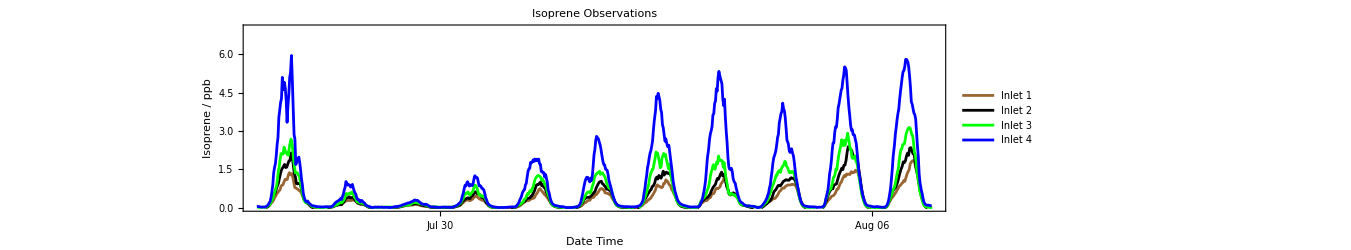

```mathematica
plot1a=DateListPlot[{isopsmooth1,isopsmooth2,isopsmooth3,isopsmooth4},
PlotRange->{Automatic,{0,7.0}}, 
PlotLabel-> "Isoprene Observations", 
LabelStyle->Directive[Black, 17],
PlotStyle->{Directive[Brown,AbsoluteThickness[2.0]],Directive[Black,AbsoluteThickness[2.0]],Directive[Green,AbsoluteThickness[2.0]],Directive[Blue,AbsoluteThickness[2.0]]},
AspectRatio->.25,
ImageSize->1000,
Joined->{True,True,True,True},
Frame -> True,
FrameLabel->{Style["Date Time",Black,17],Style["Isoprene / ppb",Black,17]},
FrameTicks -> Automatic,
PlotLegends->Placed[{"Inlet 1", "Inlet 2", "Inlet 3","Inlet 4"},{0.15,0.75}],
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["IsopObs.jpeg",plot1a]
```

IsopObs.jpeg

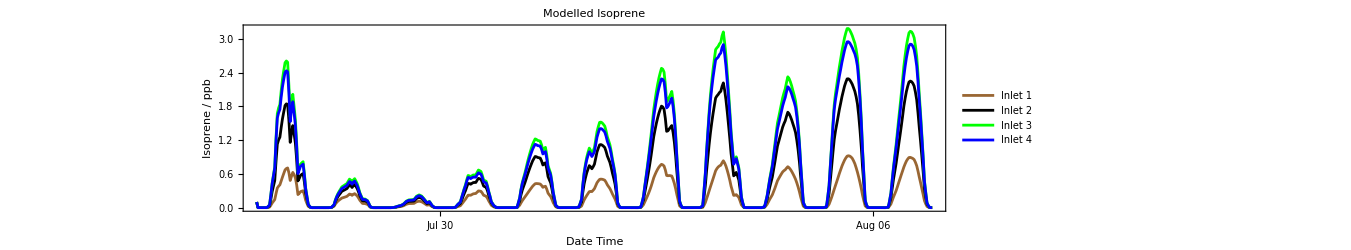

```mathematica
plot2 =DateListPlot[{box1,box13,box22,box26},PlotRange->All, 
PlotLabel-> "Modelled Isoprene", 
LabelStyle->Directive[Black, 17],
PlotStyle->{Directive[Brown,AbsoluteThickness[2.0]],Directive[Black,AbsoluteThickness[2.0]],Directive[Green,AbsoluteThickness[2.0]],Directive[Blue,AbsoluteThickness[2.0]]},
AspectRatio->.25,
ImageSize->1000,
Joined->{True,True,True,True},
Frame -> True,
FrameLabel->{Style["Date Time",Black,17],Style["Isoprene / ppb",Black,17]},
FrameTicks -> Automatic,
PlotLegends->Placed[{"Inlet 1", "Inlet 2", "Inlet 3","Inlet 4"},{0.15,0.75}],
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["Box1.csv",box1];
Export["Box13.csv",box13];
Export["Box22.csv",box22];
Export["Box26.csv",box26];
```

```mathematica
Export["IsopMod.jpeg",plot2]
```

IsopMod.jpeg

```mathematica
Directory[]
```

C:\Users\cgb36\Dropbox (Cambridge University)\iDirac - Wytham Final\CamCan Model\20190222_UpdatedModel

```mathematica
Export["measured.png",plot1,"PNG"];
Export["modelled.png",plot2,"PNG"];
```

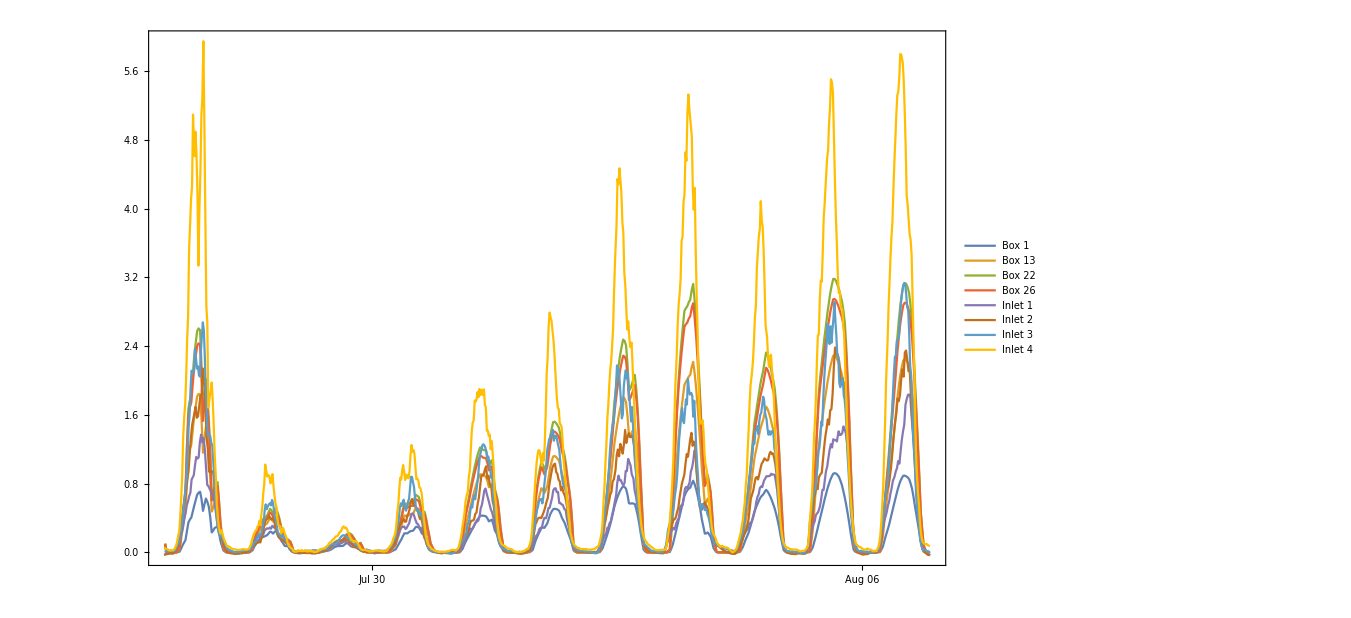

```mathematica
DateListPlot[{box1, box13,box22,box26,isopsmooth1,isopsmooth2,isopsmooth3,isopsmooth4},PlotRange->All,PlotLegends->Placed[{"Box 1","Box 13","Box 22","Box 26","Inlet 1","Inlet 2","Inlet 3","Inlet 4"},{0.23,0.85}],ImageSize->1000]
```

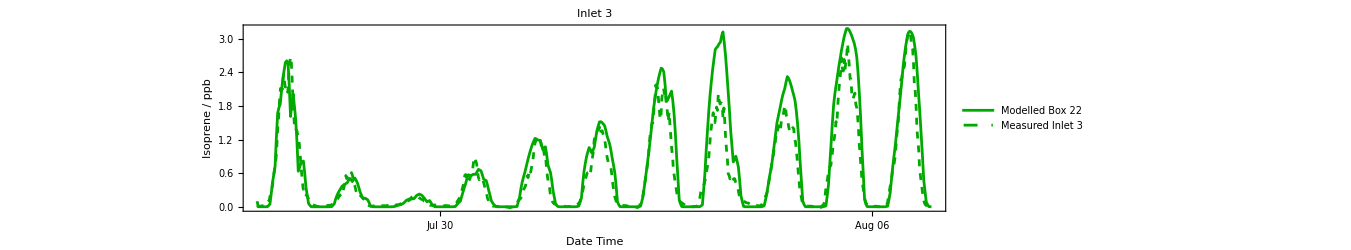

```mathematica
inlet3plot=DateListPlot[{box22,isopsmooth3},
PlotRange->All,
ImageSize->1000,
AspectRatio->.25,
PlotLabel-> "Inlet 3", 
LabelStyle->Directive[Black, 17],
PlotStyle->{Directive[Darker[Green],AbsoluteThickness[2.0]],Directive[Darker[Green],Dashed,AbsoluteThickness[2.0]]},
Joined->{True,True},
Frame -> True,
FrameLabel->{Style["Date Time",Black,17],Style["Isoprene / ppb",Black,17]},
FrameTicks -> Automatic,
PlotLegends->Placed[{"Modelled Box 22", "Measured Inlet 3"},{0.25,0.75}],
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["1inlet3.jpeg",inlet3plot];
```

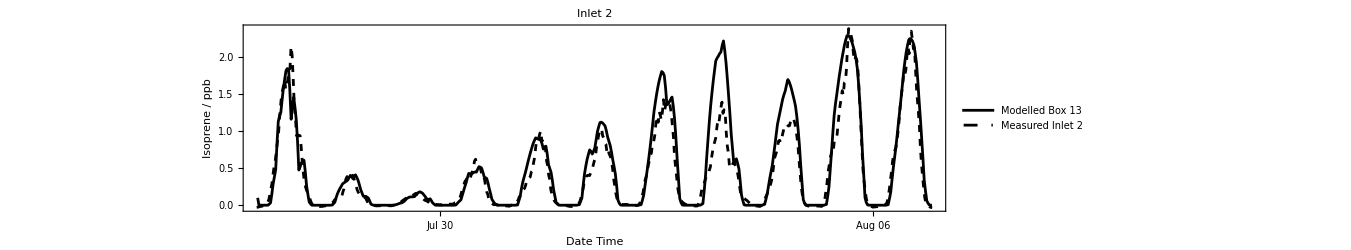

```mathematica
inlet2plot=DateListPlot[{box13,isopsmooth2},
PlotRange->All,
ImageSize->1000,
AspectRatio->.25,
PlotLabel-> "Inlet 2", 
LabelStyle->Directive[Black, 17],
PlotStyle->{Directive[Black,AbsoluteThickness[2.0]],Directive[Black,Dashed,AbsoluteThickness[2.0]]},
Joined->{True,True},
Frame -> True,
FrameLabel->{Style["Date Time",Black,17],Style["Isoprene / ppb",Black,17]},
FrameTicks -> Automatic,
PlotLegends->Placed[{"Modelled Box 13", "Measured Inlet 2"},{0.25,0.75}],
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["1inlet2.jpeg",inlet2plot];
```

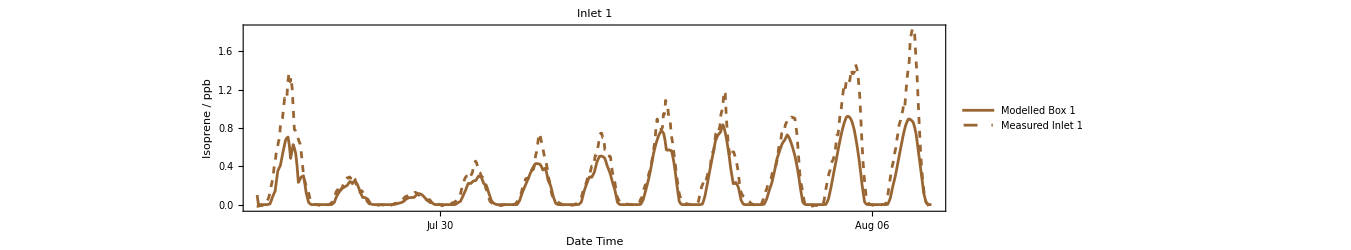

```mathematica
inlet1plot=DateListPlot[{box1,isopsmooth1},
PlotRange->All,
ImageSize->1000,
AspectRatio->.25,
PlotLabel-> "Inlet 1", 
LabelStyle->Directive[Black, 17],
PlotStyle->{Directive[Brown,AbsoluteThickness[2.0]],Directive[Brown,Dashed,AbsoluteThickness[2.0]]},
Joined->{True,True},
Frame -> True,
FrameLabel->{Style["Date Time",Black,17],Style["Isoprene / ppb",Black,17]},
FrameTicks -> Automatic,
PlotLegends->Placed[{"Modelled Box 1", "Measured Inlet 1"},{0.25,0.75}],
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["1inlet1.jpeg",inlet1plot];
```

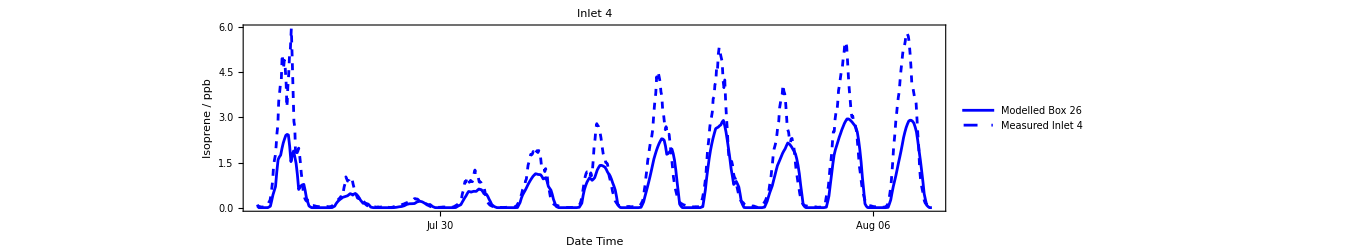

```mathematica
inlet4plot=DateListPlot[{box26,isopsmooth4},
PlotRange->All,
ImageSize->1000,
AspectRatio->.25,
PlotLabel-> "Inlet 4", 
LabelStyle->Directive[Black, 17],
PlotStyle->{Directive[Blue,AbsoluteThickness[2.0]],Directive[Blue,Dashed,AbsoluteThickness[2.0]]},
Joined->{True,True},
Frame -> True,
FrameLabel->{Style["Date Time",Black,17],Style["Isoprene / ppb",Black,17]},
FrameTicks -> Automatic,
PlotLegends->Placed[{"Modelled Box 26", "Measured Inlet 4"},{0.25,0.75}],
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["1inlet4.jpeg",inlet4plot];
```

## Inlet 1 Comparison

```mathematica
box1i=Interpolation[box1];
```

```mathematica
box1v2=Table[{i,box1i[i]},{i,t1a,t2a,1500}];
```

```mathematica
isop1i=Interpolation[isopsmooth1,InterpolationOrder->1];
isop1=Table[{i,isop1i[i]},{i,t1a,t2a,1500}];
```

```mathematica
aa=box1v2[[;;,2]];
bb=isop1[[;;,2]];
```

```mathematica
inlet1scat={aa,bb};
```

```mathematica
inlet1scattran=Transpose[inlet1scat];
```

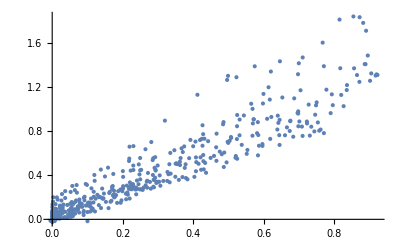

```mathematica
ListPlot[inlet1scattran]
```

```mathematica
modobsdata=LinearModelFit[inlet1scattran,x,x];
rsqinlet1=modobsdata["RSquared"];
```

LinearModelFit::ivar: {20.} is not a valid variable.

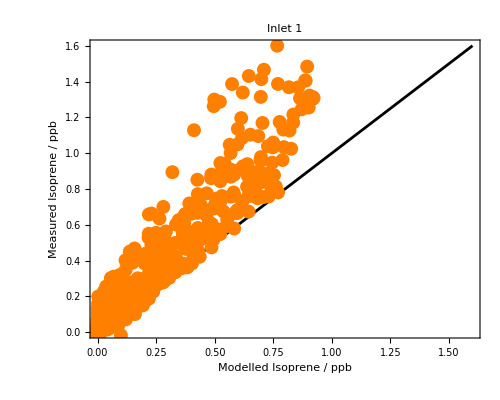

```mathematica
xmax=1.6;
ymax=xmax;

scatt1plot=ListPlot[{inlet1scattran,Table[{i,i},{i,0,xmax,.1}]},
Joined->{False,True},
PlotRange->{{0,xmax},{0,ymax}},
ImageSize->500,
AspectRatio->0.8,
PlotLabel-> "Inlet 1", 
LabelStyle->Directive[Black, 22],
PlotStyle->{Directive[Orange,PointSize[0.02]],Directive[Black,AbsoluteThickness[2.0]]},
Frame -> True,
FrameLabel->{Style["Modelled Isoprene / ppb",Black,26],Style["Measured Isoprene / ppb",Black,26]},
FrameTicks -> Automatic,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["Inlet1Comparison.jpeg",scatt1plot]
```

Inlet1Comparison.jpeg

## Inlet 2 Comparison

```mathematica
box13i=Interpolation[box13];
box13v2=Table[{i,box13i[i]},{i,t1a,t2a,1500}];
```

```mathematica
isop2i=Interpolation[isopsmooth2,InterpolationOrder->1];
isop2=Table[{i,isop2i[i]},{i,t1a,t2a,1500}];
```

```mathematica
aa=box13v2[[;;,2]];
bb=isop2[[;;,2]];
```

```mathematica
inlet2scat={aa,bb};
```

```mathematica
inlet2scattran=Transpose[inlet2scat];
```

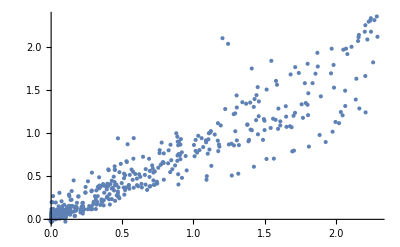

```mathematica
ListPlot[inlet2scattran]
```

```mathematica
modobsdata=LinearModelFit[inlet2scattran,x,x];
rsqinlet2=modobsdata["RSquared"];
```

LinearModelFit::ivar: {20.} is not a valid variable.

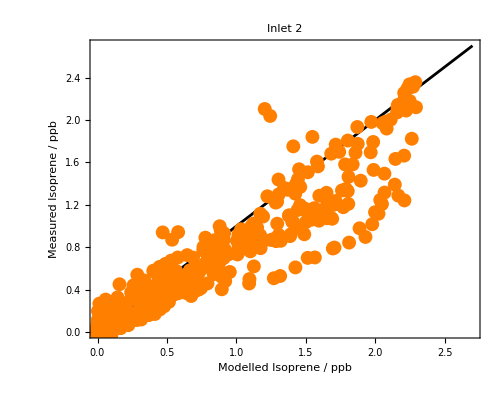

```mathematica
xmax=2.7;
ymax=xmax;

scatt2plot=ListPlot[{inlet2scattran,Table[{i,i},{i,0,xmax,.1}]},
Joined->{False,True},
PlotRange->{{0,xmax},{0,ymax}},
ImageSize->500,
AspectRatio->0.8,
PlotLabel-> "Inlet 2", 
LabelStyle->Directive[Black, 22],
PlotStyle->{Directive[Orange,PointSize[0.02]],Directive[Black,AbsoluteThickness[2.0]]},
Frame -> True,
FrameLabel->{Style["Modelled Isoprene / ppb",Black,26],Style["Measured Isoprene / ppb",Black,26]},
FrameTicks -> Automatic,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["Inlet2Comparison.jpeg",scatt2plot]
```

Inlet2Comparison.jpeg

## Inlet 3 Comparison

```mathematica
box22i=Interpolation[box22];
box22v2=Table[{i,box22i[i]},{i,t1a,t2a,1500}];
```

```mathematica
isop3i=Interpolation[isopsmooth3,InterpolationOrder->1];
isop3=Table[{i,isop3i[i]},{i,t1a,t2a,1500}];
```

```mathematica
aa3=box22v2[[;;,2]];
bb3=isop3[[;;,2]];
```

```mathematica
inlet3scat={aa3,bb3};
```

```mathematica
inlet3scattran=Transpose[inlet3scat];
```

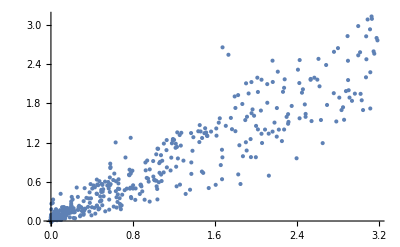

```mathematica
ListPlot[inlet3scattran]
```

```mathematica
modobsdata=LinearModelFit[inlet3scattran,x,x];
rsqinlet3=modobsdata["RSquared"];
```

LinearModelFit::ivar: {20.} is not a valid variable.

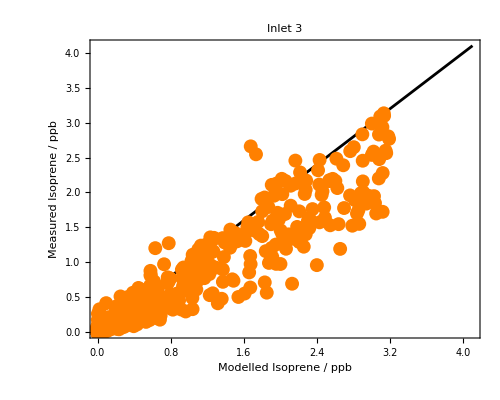

```mathematica
xmax=4.1;
ymax=xmax;
scatt3plot=ListPlot[{inlet3scattran,Table[{i,i},{i,0,xmax,.1}]},Joined->{False,True},
PlotRange->{{0,xmax},{0,ymax}},
ImageSize->500,
AspectRatio->0.8,
PlotLabel-> "Inlet 3", 
LabelStyle->Directive[Black, 22],
PlotStyle->{Directive[Orange,PointSize[0.02]],Directive[Black,AbsoluteThickness[2.0]]},
Frame -> True,
FrameLabel->{Style["Modelled Isoprene / ppb",Black,26],Style["Measured Isoprene / ppb",Black,26]},
FrameTicks -> Automatic,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["Inlet3Comparison.jpeg",scatt3plot]
```

Inlet3Comparison.jpeg

## Inlet 4 Comparison

```mathematica
box26i=Interpolation[box26];
box26v2=Table[{i,box26i[i]},{i,t1a,t2a,1200}];
```

```mathematica
isop4i=Interpolation[isopsmooth4,InterpolationOrder->1];
isop4=Table[{i,isop4i[i]},{i,t1a,t2a,1200}];
```

```mathematica
aa=box26v2[[;;,2]];
bb=isop4[[;;,2]];
```

```mathematica
inlet4scat={aa,bb};
```

```mathematica
inlet4scattran=Transpose[inlet4scat];
```

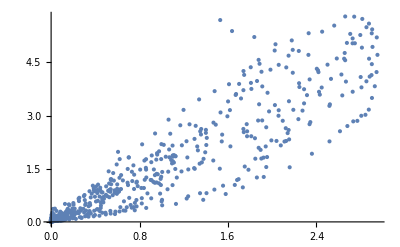

```mathematica
ListPlot[inlet4scattran]
```

```mathematica
modobsdata=LinearModelFit[inlet4scattran,x,x];
rsqinlet4=modobsdata["RSquared"];
```

LinearModelFit::ivar: {20.} is not a valid variable.

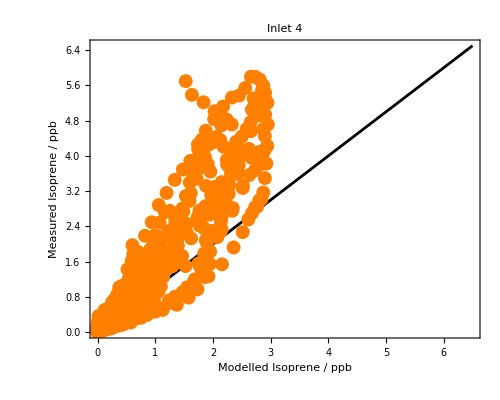

```mathematica
xmax=6.5;
ymax=xmax;
scatt4plot=ListPlot[{inlet4scattran,Table[{i,i},{i,0,xmax,.1}]},Joined->{False,True},
PlotRange->{{0,xmax},{0,ymax}},
ImageSize->500,
AspectRatio->0.8,
PlotLabel-> "Inlet 4", 
LabelStyle->Directive[Black, 22],
PlotStyle->{Directive[Orange,PointSize[0.02]],Directive[Black,AbsoluteThickness[2.0]]},
Frame -> True,
FrameLabel->{Style["Modelled Isoprene / ppb",Black,26],Style["Measured Isoprene / ppb",Black,26]},
FrameTicks -> Automatic,
BaseStyle->{FontSize->32},
LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["Inlet4Comparison.jpeg",scatt4plot]
```

Inlet4Comparison.jpeg